```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
(*<<EpidCRN`;*)
RN={0->"S","S"+"I1"->2"I1","S"+"Y1"->"Y1"+"I1","I1"->"R1","S"+"I2"->2"I2","S"+"Y2"->"Y2"+"I2","I2"->"R2","R1"+"I2"->"I2"+"Y2","R1"+"Y2"->2"Y2","Y2"->"R","R2"+"I1"->"I1"+"Y1","R2"+"Y1"->2"Y1","Y1"->"R","R1"->"S","R2"->"S","R"->"S","S"->0,"I1"->0,"Y1"->0,"R1"->0,"I2"->0,"Y2"->0,"R2"->0,"R"->0};
rts={Λ,Subscript[β, 1]  I1  S,Subscript[β, 1]  Subscript[η, 1]  Y1  S,Subscript[γ, 1]  I1,Subscript[β, 2]  I2  S,Subscript[β, 2]  Subscript[η, 2]  Y2  S,Subscript[γ, 2]  I2,Subscript[β, 2]  Subscript[σ, 2]  I2  R1,Subscript[β, 2]  Subscript[σ, 2]  Subscript[η, 2]  Y2  R1,Subscript[γ, 2]  Y2,Subscript[β, 1]  Subscript[σ, 1]  I1  R2,Subscript[β, 1]  Subscript[σ, 1]  Subscript[η, 1]  Y1  R2,Subscript[γ, 1]  Y1,Subscript[θ, 1]  R1,Subscript[θ, 2]  R2,Subscript[θ, 3]  R,μ  S,μ  I1,μ  Y1,μ  R1,μ  I2,μ  Y2,μ  R2,μ  R};
{spe,al,be,gamma,Rv,RHS,def}=extMat[RN];
var=ToExpression[spe];
RHS=gamma.rts;
par=Par[RHS,var];
(*Print["ga, be are",gamma//MatrixForm,be//MatrixForm];*)
Print["reactions and transitions: ",Transpose[{RN,rts}]//MatrixForm]
Print["RHS= ",RHS//MatrixForm]
Print["parameters: ", par];
```

reactions and transitions: (0→S | Λ
I1+S→2 I1 | I1 S β_1
S+Y1→I1+Y1 | S Y1 β_1 η_1
I1→R1 | I1 γ_1
I2+S→2 I2 | I2 S β_2
S+Y2→I2+Y2 | S Y2 β_2 η_2
I2→R2 | I2 γ_2
I2+R1→I2+Y2 | I2 R1 β_2 σ_2
R1+Y2→2 Y2 | R1 Y2 β_2 η_2 σ_2
Y2→R | Y2 γ_2
I1+R2→I1+Y1 | I1 R2 β_1 σ_1
R2+Y1→2 Y1 | R2 Y1 β_1 η_1 σ_1
Y1→R | Y1 γ_1
R1→S | R1 θ_1
R2→S | R2 θ_2
R→S | R θ_3
S→0 | S μ
I1→0 | I1 μ
Y1→0 | Y1 μ
R1→0 | R1 μ
I2→0 | I2 μ
Y2→0 | Y2 μ
R2→0 | R2 μ
R→0 | R μ)

RHS= (Λ-S μ-I1 S β_1-I2 S β_2-S Y1 β_1 η_1-S Y2 β_2 η_2+R1 θ_1+R2 θ_2+R θ_3
-I1 μ+I1 S β_1-I1 γ_1+S Y1 β_1 η_1
-Y1 μ-Y1 γ_1+I1 R2 β_1 σ_1+R2 Y1 β_1 η_1 σ_1
-R1 μ+I1 γ_1-R1 θ_1-I2 R1 β_2 σ_2-R1 Y2 β_2 η_2 σ_2
-I2 μ+I2 S β_2-I2 γ_2+S Y2 β_2 η_2
-Y2 μ-Y2 γ_2+I2 R1 β_2 σ_2+R1 Y2 β_2 η_2 σ_2
-R2 μ+I2 γ_2-R2 θ_2-I1 R2 β_1 σ_1-R2 Y1 β_1 η_1 σ_1
-R μ+Y1 γ_1+Y2 γ_2-R θ_3)

parameters: {Λ,μ,β_1,β_2,γ_1,γ_2,η_1,η_2,θ_1,θ_2,θ_3,σ_1,σ_2}

```mathematica
spe
```

{S,I1,Y1,R1,I2,Y2,R2,R}

```mathematica
Nspe=Length[spe];
xi=Table[x[i],{i,1,Nspe}];
xit=Table[x[i][t],{i,1,Nspe}];
derxit=Table[x[i]'[t],{i,1,Nspe}];
spe2xit=Thread[var->xit];
diffeqs=Thread[derxit==RHS/.spe2xit];
DFE={0,0,15/10,3/10,1,1,1,1,1/10000,1/10000,1/10000,25/10,3};
A1GavishRabiu={0,0,15/100,2,1,1,1,1,1/10000,1/10000,1/10000,25/10,3};
A2GavishRabiu={0,0,15/10,2,1,1,1,1,1/10000,1/10000,1/10000,25/10,3};
A3GavishRabiu={0,0,3,2,1,1,1,1,1/10000,1/10000,1/10000,25/10,3};
```

```mathematica
x0d
```

{0.49,0.002,0.002,0.002,0.000049995,0.002,0.49995,0.002}

(x[1.]'[t]==6.77626×10^-21
x[2.]'[t]==0.
x[3.]'[t]==0.
x[4.]'[t]==0.
x[5.]'[t]==0.
x[6.]'[t]==0.
x[7.]'[t]==-6.77626×10^-21
x[8.]'[t]==0.)

(x[1.]'[t]==-0.0002294
x[2.]'[t]==-0.00017006
x[3.]'[t]==-0.000125007
x[4.]'[t]==0.00019968
x[5.]'[t]==0.0001995
x[6.]'[t]==-0.0001997
x[7.]'[t]==-0.0000749925
x[8.]'[t]==0.00039998)

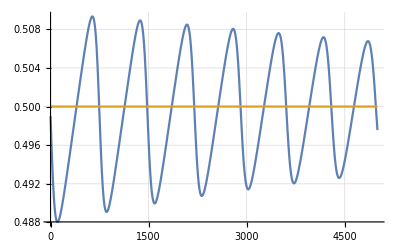
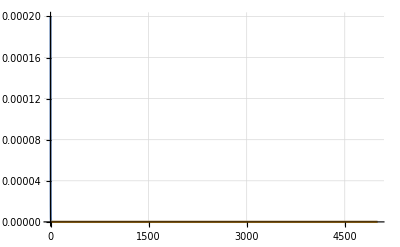
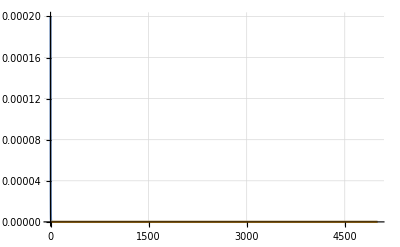
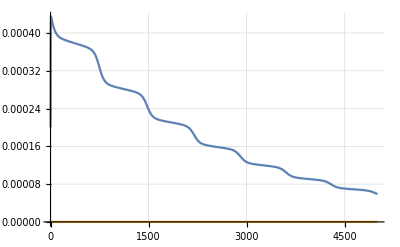
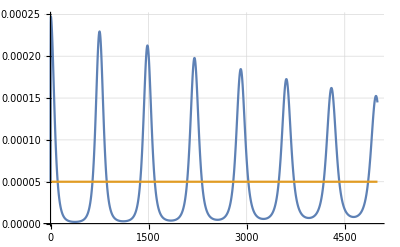
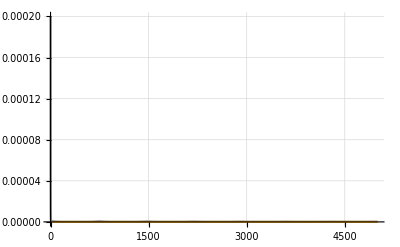
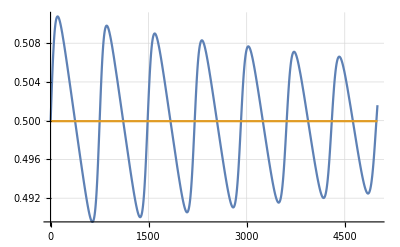
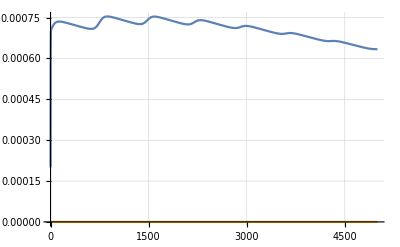
{{S,-Graphics-},{I1,-Graphics-},{Y1,-Graphics-},{R1,-Graphics-},{I2,-Graphics-},{Y2,-Graphics-},{R2,-Graphics-},{R,-Graphics-}}

A1init.pdf

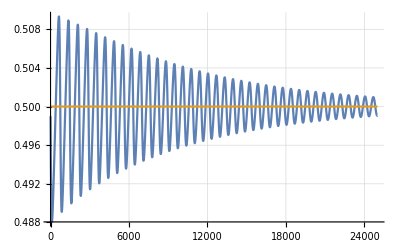
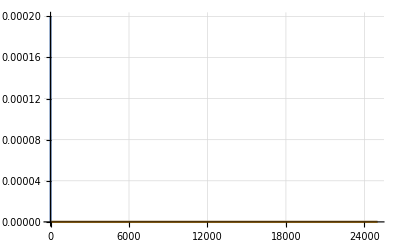
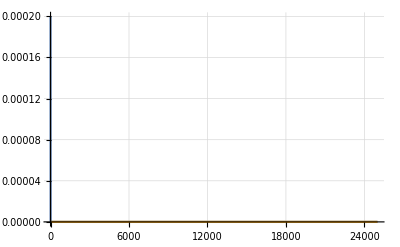
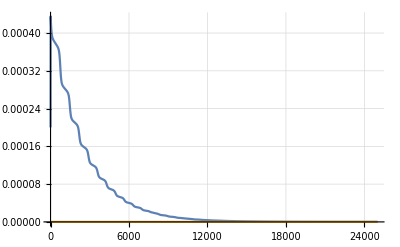
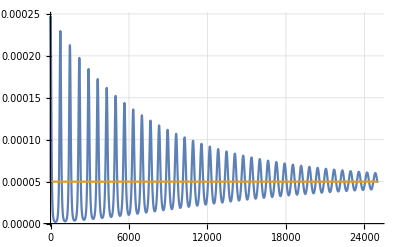
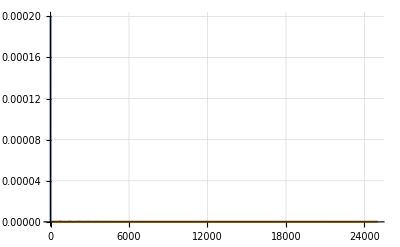
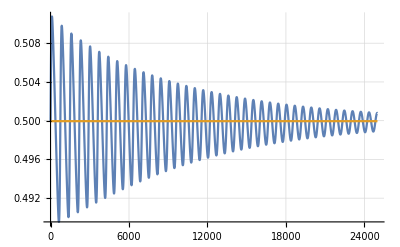
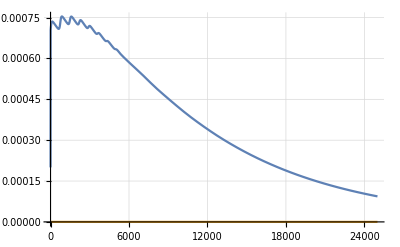
{{S,-Graphics-},{I1,-Graphics-},{Y1,-Graphics-},{R1,-Graphics-},{I2,-Graphics-},{Y2,-Graphics-},{R2,-Graphics-},{R,-Graphics-}}

A1.pdf

```mathematica
(* A1 eqiulibrium: *)
x0={1/2,0,0,0,0.000049995,0,0.49995,0};
(* goes to A1 Equilibrium through oscillation *)
d=0.001;
x0d={1/2-d,d/5,d/5,d/5,0.000049995,d/5,0.49995,d/5};
parsub=Thread[par->A1GavishRabiu];
initcond=Thread[xit==x0]/.t->0;
Print[diffeqs/.parsub/.Thread[xit->x0]//N//MatrixForm];
tmax=25000;
s=NDSolve[Join[diffeqs/.parsub,initcond],xit,{t,0,tmax},Method->{"BDF"},PrecisionGoal->15];
initcond=Thread[xit==x0d]/.t->0;
Print[diffeqs/.parsub/.Thread[xit->x0d]//N//MatrixForm];
sd=NDSolve[Join[diffeqs/.parsub,initcond],xit,{t,0,tmax},Method->{"BDF"}];
Table[{var[[i]],Plot[{Evaluate[xit[[i]]/.sd],Evaluate[xit[[i]]/.s]},{t,0,tmax/5},PlotRange->All,GridLines->Automatic]},{i,1,8}]
Export["A1init.pdf",%]
Table[{var[[i]],Plot[{Evaluate[xit[[i]]/.sd],Evaluate[xit[[i]]/.s]},{t,0,tmax},PlotRange->All,GridLines->Automatic]},{i,1,8}]
Export["A1.pdf",%]
```

(x[1.]'[t]==2.71051×10^-20
x[2.]'[t]==0.
x[3.]'[t]==-3.38813×10^-21
x[4.]'[t]==-3.38813×10^-21
x[5.]'[t]==5.0822×10^-21
x[6.]'[t]==-6.77626×10^-21
x[7.]'[t]==0.
x[8.]'[t]==-1.35525×10^-20)

(x[1.]'[t]==3.02904×10^-7
x[2.]'[t]==-8.02738×10^-8
x[3.]'[t]==-3.38813×10^-21
x[4.]'[t]==-3.38813×10^-21
x[5.]'[t]==-1.2263×10^-7
x[6.]'[t]==-6.77626×10^-21
x[7.]'[t]==0.
x[8.]'[t]==-1.×10^-7)

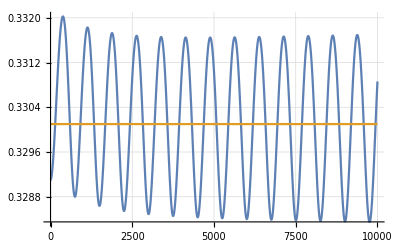
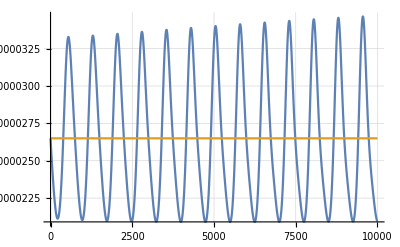
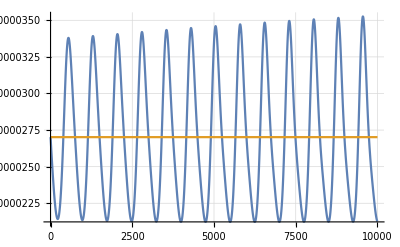
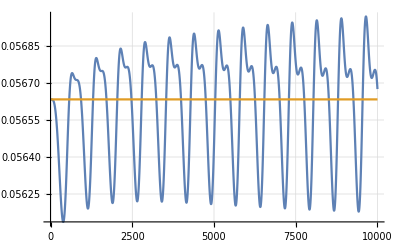
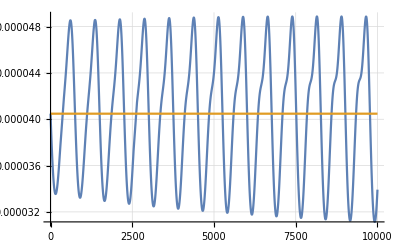
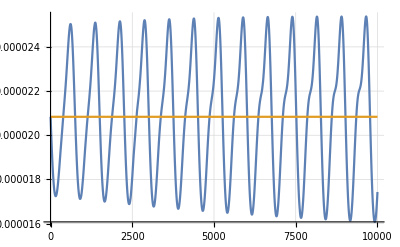
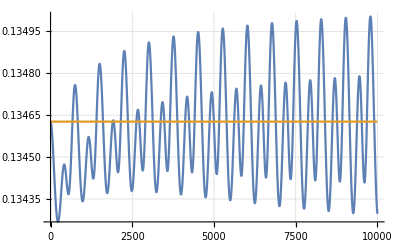
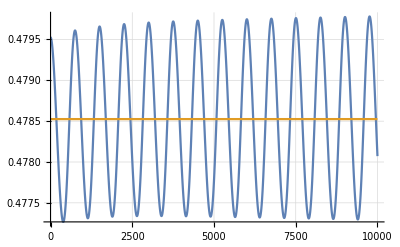
{{S,-Graphics-},{I1,-Graphics-},{Y1,-Graphics-},{R1,-Graphics-},{I2,-Graphics-},{Y2,-Graphics-},{R2,-Graphics-},{R,-Graphics-}}

A2init.pdf

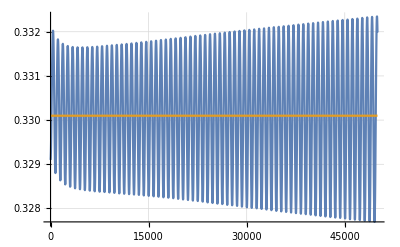
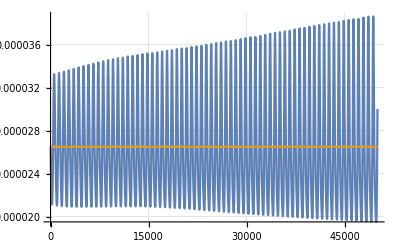
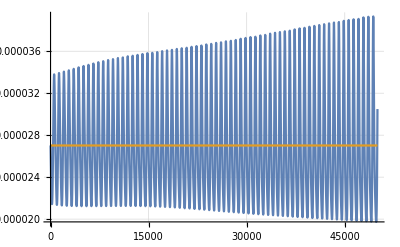
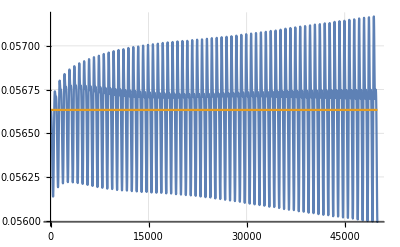
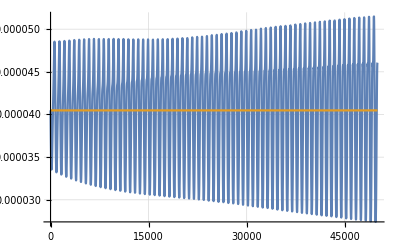
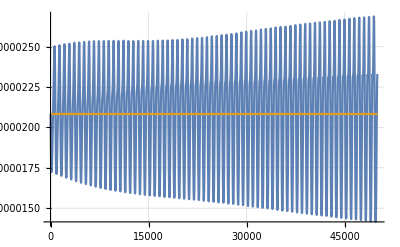
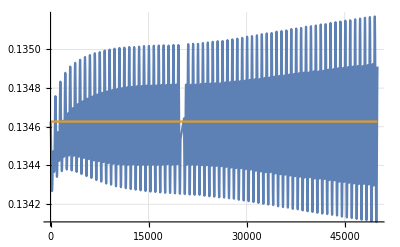
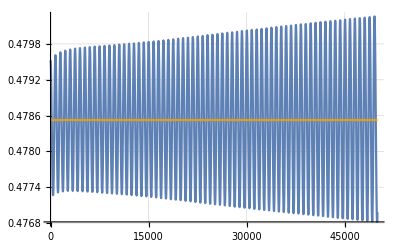
{{S,-Graphics-},{I1,-Graphics-},{Y1,-Graphics-},{R1,-Graphics-},{I2,-Graphics-},{Y2,-Graphics-},{R2,-Graphics-},{R,-Graphics-}}

A2.pdf

```mathematica
(* A2 equilibrium *)
A2eq={S->0.3300993868102641,I1->0.000026498342231681548,Y1->0.00002701754478189108,R1->0.056633537729911976,I2->0.00004048023597614718,Y2->0.00002083498845869036,R2->0.13462691194256102};
x0=var/.A2eq;
x0=x0/.R->(1-Total[x0[[1;;7]]]);
d=0.001;
x0d=x0;
x0d[[1]]=x0d[[1]]-d;
x0d[[8]]=x0d[[8]]+d;

parsub=Thread[par->A2GavishRabiu];
initcond=Thread[xit==x0]/.t->0;
Print[diffeqs/.parsub/.Thread[xit->x0]//N//MatrixForm];
tmax=50000;
s=NDSolve[Join[diffeqs/.parsub,initcond],xit,{t,0,tmax},Method->{"BDF"},PrecisionGoal->15];
initcond=Thread[xit==x0d]/.t->0;
Print[diffeqs/.parsub/.Thread[xit->x0d]//N//MatrixForm];
sd=NDSolve[Join[diffeqs/.parsub,initcond],xit,{t,0,tmax},Method->{"BDF"}];
Table[{var[[i]],Plot[{Evaluate[xit[[i]]/.sd],Evaluate[xit[[i]]/.s]},{t,0,tmax/5},PlotRange->All,GridLines->Automatic]},{i,1,8}]
Export["A2init.pdf",%]
Table[{var[[i]],Plot[{Evaluate[xit[[i]]/.sd],Evaluate[xit[[i]]/.s]},{t,0,tmax},PlotRange->All,GridLines->Automatic]},{i,1,8}]
Export["A2.pdf",%]
```

(x[1.]'[t]==6.77626×10^-21
x[2.]'[t]==6.77626×10^-21
x[3.]'[t]==0.
x[4.]'[t]==-1.35525×10^-20
x[5.]'[t]==3.38813×10^-21
x[6.]'[t]==6.77626×10^-21
x[7.]'[t]==-1.01644×10^-20
x[8.]'[t]==0.)

(x[1.]'[t]==4.58226×10^-7
x[2.]'[t]==-2.20681×10^-7
x[3.]'[t]==0.
x[4.]'[t]==-1.35525×10^-20
x[5.]'[t]==-1.37545×10^-7
x[6.]'[t]==6.77626×10^-21
x[7.]'[t]==-1.01644×10^-20
x[8.]'[t]==-1.×10^-7)

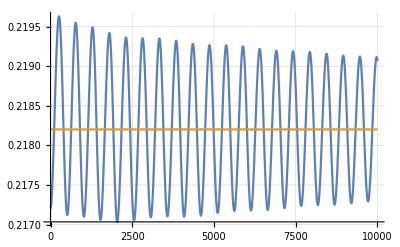
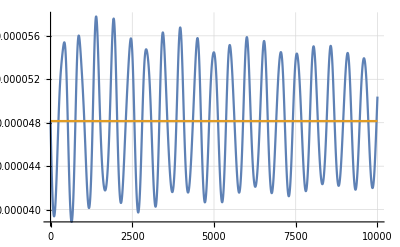
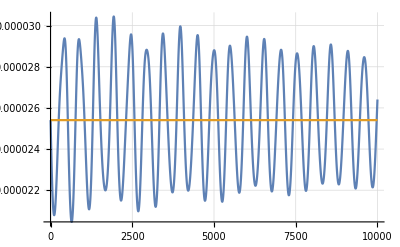
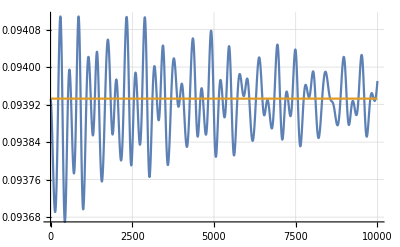
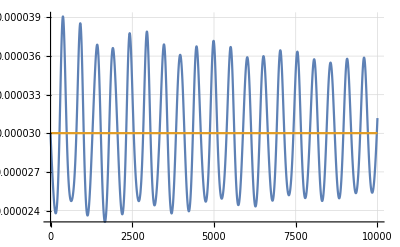
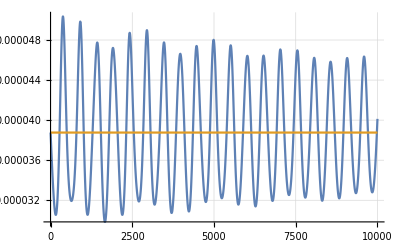
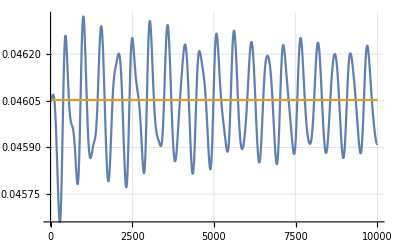
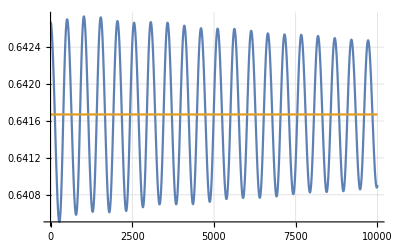
{{S,-Graphics-},{I1,-Graphics-},{Y1,-Graphics-},{R1,-Graphics-},{I2,-Graphics-},{Y2,-Graphics-},{R2,-Graphics-},{R,-Graphics-}}

A3init.pdf

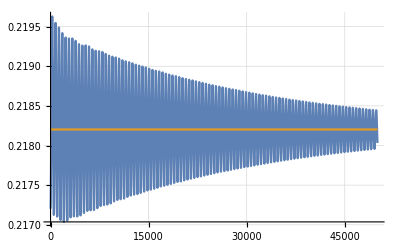
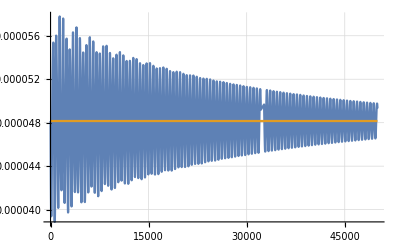
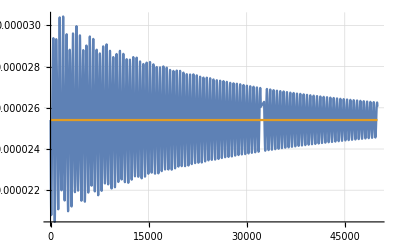
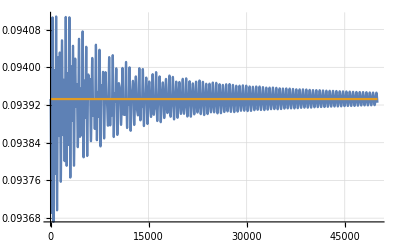
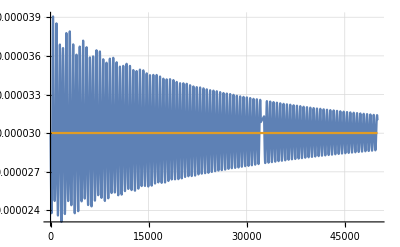
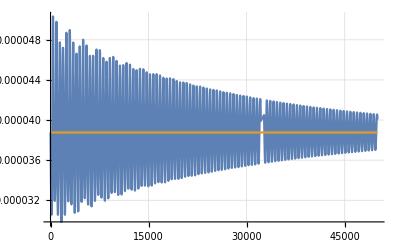
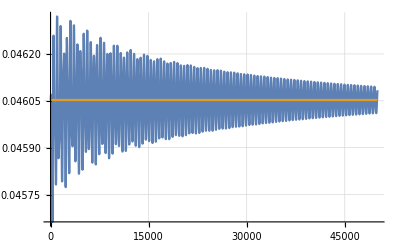
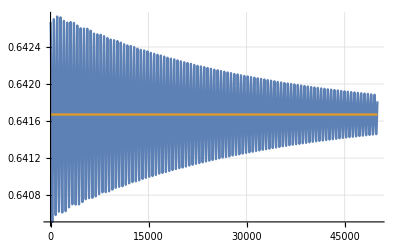
{{S,-Graphics-},{I1,-Graphics-},{Y1,-Graphics-},{R1,-Graphics-},{I2,-Graphics-},{Y2,-Graphics-},{R2,-Graphics-},{R,-Graphics-}}

A3.pdf

```mathematica
(* A3 equilibrium *)
A3eq={S->0.2182020958840389,I1->0.000048153039911599245,Y1->0.000025407267741891635,R1->0.09393263470532039,I2->0.000030012517239863404,Y2->0.00003875977644106721,R2->0.046052494979717785};
x0=var/.A3eq;
x0=x0/.R->(1-Total[x0[[1;;7]]]);
d=0.001;
x0d=x0;
x0d[[1]]=x0d[[1]]-d;
x0d[[8]]=x0d[[8]]+d;
parsub=Thread[par->A3GavishRabiu];
initcond=Thread[xit==x0]/.t->0;
Print[diffeqs/.parsub/.Thread[xit->x0]//N//MatrixForm];
tmax=50000;
s=NDSolve[Join[diffeqs/.parsub,initcond],xit,{t,0,tmax},Method->{"BDF"},PrecisionGoal->15];
initcond=Thread[xit==x0d]/.t->0;
Print[diffeqs/.parsub/.Thread[xit->x0d]//N//MatrixForm];
sd=NDSolve[Join[diffeqs/.parsub,initcond],xit,{t,0,tmax},Method->{"BDF"}];
Table[{var[[i]],Plot[{Evaluate[xit[[i]]/.sd],Evaluate[xit[[i]]/.s]},{t,0,tmax/5},PlotRange->All,GridLines->Automatic]},{i,1,8}]
Export["A3init.pdf",%]
Table[{var[[i]],Plot[{Evaluate[xit[[i]]/.sd],Evaluate[xit[[i]]/.s]},{t,0,tmax},PlotRange->All,GridLines->Automatic]},{i,1,8}]
Export["A3.pdf",%]
```

```mathematica
var
```

{S,I1,Y1,R1,I2,Y2,R2,R}

```mathematica
RHSGavishpaper=RHS/.Λ->0/.μ->0/.Subscript[θ, 1]->θ/.Subscript[θ, 2]->θ/.Subscript[θ, 3]->θ/.Subscript[γ, 1]->1/.Subscript[γ, 2]->1/. Subscript[η, 1]->1/. Subscript[η, 2]->1/.R->1-S-I1-I2-Y1-Y2-R1-R2;
RHSGavishpaper=RHSGavishpaper[[1;;7]]
```

{R1 θ+R2 θ+(1-I1-I2-R1-R2-S-Y1-Y2) θ-I1 S β_1-S Y1 β_1-I2 S β_2-S Y2 β_2,-I1+I1 S β_1+S Y1 β_1,-Y1+I1 R2 β_1 σ_1+R2 Y1 β_1 σ_1,I1-R1 θ-I2 R1 β_2 σ_2-R1 Y2 β_2 σ_2,-I2+I2 S β_2+S Y2 β_2,-Y2+I2 R1 β_2 σ_2+R1 Y2 β_2 σ_2,I2-R2 θ-I1 R2 β_1 σ_1-R2 Y1 β_1 σ_1}

```mathematica
(* DFE *)
Solve[Thread[(RHSGavishpaper/.Thread[{I1,Y1,R1,I2,Y2,R2,R}->0])==0],{S}]
```

{{S→1}}

```mathematica
(* single strain equilibrium *)
E2=Solve[Thread[(RHSGavishpaper/.Thread[{Y2,I1,Y1,R1,R}->0])==0],{I2,S,R2}]
parsub=Thread[par->A1GavishRabiu];
E2/.parsub/.θ->0.0001
```

{{I2→0,S→1,R2→0},{I2→(θ (-1+β_2))/((1+θ) β_2),S→1/β_2,R2→(-1+β_2)/((1+θ) β_2)}}

{{I2→0,S→1,R2→0},{I2→0.000049995,S→1/2,R2→0.49995}}

```mathematica
(* multi strain equilibrium A3 only numerically *)
parsub=Thread[par->A3GavishRabiu];
NSolve[Thread[(RHSGavishpaper/.parsub/.θ->0.0001)==0],{S,I1,Y1,R1,I2,Y2,R2}]
```

{{S→1.66669,I1→-0.0000666676,Y1→0.0000533342,R1→-0.666676,I2→0,Y2→0,R2→-0.533342},{S→1.66669,I1→-0.0000666676,Y1→0.0000533342,R1→-0.666676,I2→0,Y2→0,R2→-0.533342},{S→1.50003,I1→0,Y1→0,R1→-0.333342,I2→-0.0000500008,Y2→0.0000333342,R2→-0.500008},{S→1.50003,I1→0,Y1→0,R1→-0.333342,I2→-0.0000500008,Y2→0.0000333342,R2→-0.500008},{S→1.50003,I1→0,Y1→0,R1→-0.333342,I2→-0.0000500008,Y2→0.0000333342,R2→-0.500008},{S→1.50002,I1→0,Y1→0,R1→-0.333342,I2→-0.0000500008,Y2→0.0000333342,R2→-0.500008},{S→1.46268,I1→-4.7936×10^-6,Y1→3.70118×10^-6,R1→-0.320892,I2→-0.0000414726,Y2→0.0000272956,R2→-0.451737},{S→1.46268,I1→-4.7936×10^-6,Y1→3.70118×10^-6,R1→-0.320892,I2→-0.0000414726,Y2→0.0000272956,R2→-0.451737},{S→1.,I1→0,Y1→0,R1→0,I2→0,Y2→0,R2→0},{S→0.5,I1→0,Y1→0,R1→0,I2→0.000049995,Y2→0,R2→0.49995},{S→0.333333,I1→0.00006666,Y1→0,R1→0.6666,I2→0,Y2→0,R2→0},{S→0.218202,I1→0.000048153,Y1→0.0000254073,R1→0.0939326,I2→0.0000300125,Y2→0.0000387598,R2→0.0460525}}

```mathematica
(* multi strain equilibrium A2 only numerically *)
parsub=Thread[par->A2GavishRabiu];
NSolve[Thread[(RHSGavishpaper/.parsub/.θ->0.0001)==0],{S,I1,Y1,R1,I2,Y2,R2}]
```

{{S→1.66671,I1→-0.0000666684,Y1→0.0000400018,R1→-0.666684,I2→0,Y2→0,R2→-0.400018},{S→1.66671,I1→-0.0000666684,Y1→0.0000400018,R1→-0.666684,I2→0,Y2→0,R2→-0.400018},{S→1.66671,I1→-0.0000666684,Y1→0.0000400018,R1→-0.666684,I2→0,Y2→0,R2→-0.400018},{S→1.66671,I1→-0.0000666684,Y1→0.0000400018,R1→-0.666684,I2→0,Y2→0,R2→-0.400018},{S→1.50003,I1→0,Y1→0,R1→-0.333342,I2→-0.0000500008,Y2→0.0000333342,R2→-0.500008},{S→1.50002,I1→0,Y1→0,R1→-0.333342,I2→-0.0000500008,Y2→0.0000333342,R2→-0.500008},{S→1.3565,I1→-0.0000163903,Y1→8.33509×10^-6,R1→-0.2855,I2→-0.0000192583,Y2→0.0000121597,R2→-0.275933},{S→1.3565,I1→-0.0000163903,Y1→8.33509×10^-6,R1→-0.2855,I2→-0.0000192583,Y2→0.0000121597,R2→-0.275933},{S→1.,I1→0,Y1→0,R1→0,I2→0,Y2→0,R2→0},{S→0.666667,I1→0.00003333,Y1→0,R1→0.3333,I2→0,Y2→0,R2→0},{S→0.5,I1→0,Y1→0,R1→0,I2→0.000049995,Y2→0,R2→0.49995},{S→0.330099,I1→0.0000264983,Y1→0.0000270175,R1→0.0566335,I2→0.0000404802,Y2→0.000020835,R2→0.134627}}